```mathematica
D[ⅇ^(-1/2 x^2/σ^2),{x,2}]//Simplify
```

(ⅇ^(-x^2/(2 σ^2)) (x^2-σ^2))/σ^4

```mathematica
ⅇ^(-x^2/(2 σ^2))/.x->σ//N
```

0.606531

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->10};
```

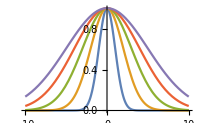

~/Desktop/bell.png

```mathematica
Plot[Evaluate@Table[ⅇ^(-1/2 x^2/σ^2),{σ,1,5}],{x,-10,10},PlotLegends->Placed[MaTeX[Table["\\sigma="<>ToString[i],{i,5}],FontSize->10],Right],AxesLabel->MaTeX[{"x","e^{-\\frac{1}{2}\\frac{x^2}{\\sigma^2}}"},FontSize->10],BaseStyle->texStyle,ImageSize->200]
Export["~/Desktop/bell.png",%,ImageResolution->800]
```

```mathematica
∫x^2 ⅇ^(-1/2 x^2)ⅆx
∫ ⅇ^(-1/2 x^2)ⅆx+D[ⅇ^(-1/2 x^2),x]
```

-ⅇ^(-x^2/2) x+√(π/2) Erf[x/(√2)]

-ⅇ^(-x^2/2) x+√(π/2) Erf[x/(√2)]

```mathematica
2/(√(2π)σ)∫ ⅇ^(-1/2(x/σ)^2)ⅆx
```

Erf[x/(√2 σ)]

MaTeX::texerr: Error while running LaTeX.
! Missing $ inserted.
!  ==> Fatal error occurred, no output PDF file produced!

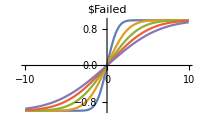

```mathematica
Plot[Evaluate@Table[Erf[x/(√2 σ)],{σ,1,5}],{x,-10,10},PlotLegends->Placed[MaTeX[Table["\\sigma="<>ToString[i],{i,5}],FontSize->10],Right],AxesLabel->MaTeX[{"x","\\text{Erf}\\left(\\frac{x}{\\sqrt{2}\\sigma}\\right)"},FontSize->10],BaseStyle->texStyle,ImageSize->200]
```